This Mathematica notebook compares a simple Weizsacker-Wiliams estimate of the A’ production cross-section to the results from MadGraph.  The WW differential xsec is taken from (5) of arXiv:1209.6083 (Andreas et al 2012)

```mathematica
doExport=False; (*Keep this false to avoid accidental overwrite of pdf*)
```

## WW Cross-section calculation

## Constants & Units

```mathematica
me=0.000511 GeV; (* electron mass in GeV *)
cm=5.0677 10^13 GeV^-1;
α=1/137.0;

NAvo=6*10^(23)/mole; (* Avogadro's number in units of 1/mol *)
NoOfElectron[time_,intensity_]:=time*intensity
barn=10^-24 cm^2;
inCM={GeV->5.0677 10^13/CM};
toPB=pb/(10^-12 barn);
Coulomb=1/(1.6 10^-19);
μM=10^-4 CM;
```

Material Properties – Tungsten

```mathematica
Z[W]=74; (* Atomic number of material; tungsten = 74 *)
A[W]=184 g/mole; (* Atomic weight in g/mol of material; tungsten = 184 *)
Xzero[W]=6.76 g/cm^2; (* Unit radiation length of material in g/cm^2; tungsten = 6.76 *)
ρ[W]=19.3 g/cm^3;(* Density of target material in g/cm^3 *)
```

```mathematica
RadiationLength[x_]:=Xzero[x]/ρ[x]/.inCM
```

Chi and Form Factors (init)

```mathematica
W2AtomicNuclearZ2[t_,a_,d_,Z_]:=Z^2 1/(1+t/d)^2 1/((1+(t a^2)^-1)^2)
```

```mathematica
W2AtomicProtonZ[t_,a_,Z_,Mp_:0.938 GeV,μp_:2.79,TZ_:0.71 GeV^2]:=Z  1/((1+(t a^2)^-1)^2) (1+t/(4 Mp^2) (μp^2-1))/(1+t/TZ)^4
```

```mathematica
ChiZ[m_,EB_,El_,x_:1]:=Module[{tmin,tmax,aEl,aIn,d},
tmin=(m^2/(2 EB x))^2;tmax=m^2;
aEl=111 Z[El]^(-1/3)/me;aIn=773 Z[El]^(-2/3)/me;
d=0.164 A[El]^(-2/3) GeV^2/.mole->g;
NIntegrate[(t GeV^2-tmin)/(t^2 GeV^4) (W2AtomicNuclearZ2[t GeV^2,aEl,d,Z[El]]+W2AtomicProtonZ[t GeV^2,aIn,Z[El]]) GeV^2,{t,tmin/GeV^2,tmax/GeV^2}]]
```

Cross-section formulas

```mathematica
DsigmaDx[ϵ_,mA_,EBeam_,x_,TargetNucleus_]:=4 α^3 ϵ^2 *ChiZ[mA,EBeam,TargetNucleus] √(1-mA^2/EBeam^2)*(1-x+1/3*x^2)/(mA^2 (1-x)/x+me^2 x)
```

```mathematica
sigma[ϵ_,mA_,EBeam_,TargetNucleus_]:=If[(mA+me)/EBeam>1,0,1/GeV^2 NIntegrate[GeV^2 DsigmaDx[ϵ,mA,EBeam,x,TargetNucleus],{x,0,1-Max[me/EBeam,mA/EBeam]},PrecisionGoal->4]] toPB
```

```mathematica
wwxsectable=Table[{10^mmev,sigma[1,10^mmev  GeV,4 GeV,W]},{mmev,-3,0.4,0.2}]
```

{{0.001,1.27923×10^13 pb},{0.00158489,8.04417×10^12 pb},{0.00251189,4.72787×10^12 pb},{0.00398107,2.60874×10^12 pb},{0.00630957,1.34067×10^12 pb},{0.01,6.18972×10^11 pb},{0.0158489,2.44932×10^11 pb},{0.0251189,8.51003×10^10 pb},{0.0398107,2.73991×10^10 pb},{0.0630957,8.23909×10^9 pb},{0.1,2.26947×10^9 pb},{0.158489,5.53113×10^8 pb},{0.251189,1.105×10^8 pb},{0.398107,1.5094×10^7 pb},{0.630957,1.01749×10^6 pb},{1.,39913.6 pb},{1.58489,1664.72 pb},{2.51189,14.5003 pb}}

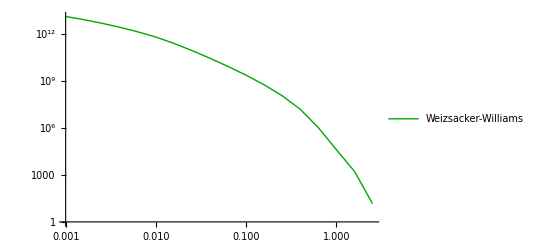

```mathematica
wwplot=ListLogLogPlot[wwxsectable/.pb->1,Joined->True,PlotStyle->Darker[Green],PlotLegends->LineLegend[{"Weizsacker-Williams"}]]
```

## MadGraph xsec read from “Integrated Weight” line in lhe files

```mathematica
xsecInclusive = Drop[Import["~/LDMXAnalysis/SignalMC/4GeVInclusive/xsectable"],1]
```

{{0.025,9.3263×10^10},{0.1,2.7164×10^9},{0.2,2.8461×10^8},{0.5,3.6372×10^6},{1.,22995.},{1.5,681.66}}

NOTE: mA=0.01 mass point in the Inclusive category was actually an off-shell A’, so don’t want to compare that cross-section to on-shell A’ xsec.

```mathematica
xsecNoDecay = Import["~/LDMXAnalysis/SignalMC/4GeV_nodecay/xsectable","Table"]
```

{{0.001,1.8259×10^13},{0.001,1.8151×10^13},{0.001,1.8216×10^13},{0.001,1.823×10^13},{0.001,1.82×10^13},{0.005,2.1475×10^12},{0.005,2.1679×10^12},{0.005,2.1596×10^12},{0.005,2.1701×10^12},{0.005,2.1731×10^12},{0.01,6.3388×10^11},{0.01,6.4016×10^11},{0.01,6.3535×10^11},{0.01,6.3446×10^11},{0.01,6.3719×10^11},{0.02,1.531×10^11},{0.02,1.5441×10^11},{0.02,1.5317×10^11},{0.02,1.5318×10^11},{0.02,1.5421×10^11},{0.04,3.051×10^10},{0.04,3.115×10^10},{0.04,3.1189×10^10},{0.04,3.1171×10^10},{0.04,3.0493×10^10},{0.07,7.3968×10^9},{0.07,7.4267×10^9},{0.07,7.4217×10^9},{0.07,7.3794×10^9},{0.07,7.4162×10^9},{0.1,2.7439×10^9},{0.1,2.7178×10^9},{0.1,2.7438×10^9},{0.1,2.6835×10^9},{0.1,2.672×10^9},{0.2,2.8101×10^8},{0.2,2.8602×10^8},{0.2,2.8514×10^8},{0.2,2.8635×10^8},{0.2,2.862×10^8},{0.4,1.355×10^7},{0.4,1.3522×10^7},{0.4,1.3456×10^7},{0.4,1.3498×10^7},{0.4,1.3444×10^7},{0.7,348260.},{0.7,347770.},{0.7,341790.},{0.7,347850.},{0.7,347880.},{1.,22903.},{1.,22708.},{1.,22985.},{1.,23006.},{1.,22811.},{1.5,680.62},{1.5,679.87},{1.5,682.12},{1.5,680.24},{1.5,678.55}}

## Comparison Plot

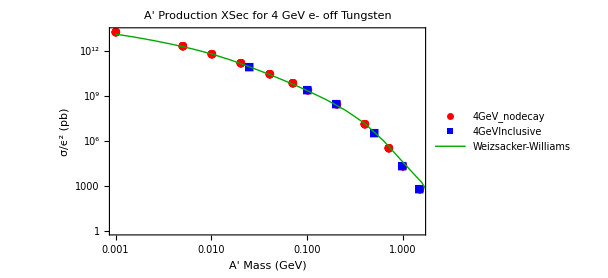

```mathematica
xsecComparison = Show[ListLogLogPlot[{xsecNoDecay,xsecInclusive},PlotStyle->{Red,Blue},PlotMarkers->{Automatic,Medium},PlotLegends->PointLegend[{"4GeV_nodecay","4GeVInclusive"},LegendMarkers->Automatic]],wwplot,Frame->True,FrameLabel->{"A' Mass (GeV)", "σ/ϵ^2 (pb)"},PlotLabel->Style["A' Production XSec for 4 GeV e- off Tungsten",16],LabelStyle->14,ImageSize->450]
```

```mathematica
If[doExport,Export["LDMXAnalysis/SignalMC/xsec_checks/xsecComparison.pdf",xsecComparison]]
```

LDMXAnalysis/SignalMC/xsec_checks/xsecComparison.pdf